```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{3}]];
hmfi = Interpolation[hmf]
```

16
InterpolatingFunction[{{0.01, 20.}, {1., 1. 10  }}, <>]

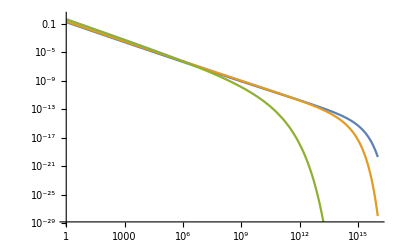

```mathematica
LogLogPlot[{hmfi[0.01,m],hmfi[1.,m],hmfi[10.,m]},{m,1.,1.*^16}]
```